*************************************随机信号分析(第5版) 李晓峰*************************************

=======================================P32 实验1=======================================

```mathematica
X=ExponentialDistribution[1/2]
```

ExponentialDistribution[1/2]

```mathematica
Mean[X]
```

2

```mathematica
Variance[X]
```

4

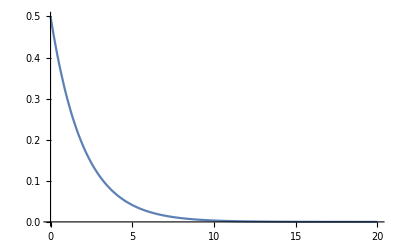

```mathematica
Plot[PDF[ExponentialDistribution[1/2],x],{x,0,20},PlotRange->All]
```

=======================================P32 实验2=======================================

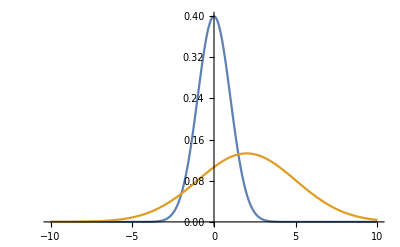

```mathematica
Plot[{PDF[NormalDistribution[0,1],x],PDF[NormalDistribution[2,3],x]},{x,-10,10},PlotRange->All]
```

=======================================P32 实验3=======================================

```mathematica
f=Exp[-2/3 (x^2-(x y)/2+y^2/4)]/(2 π √3)
```

(ⅇ^(-2/3 (x^2-(x y)/2+y^2/4)))/(2 √3 π)

```mathematica
(ⅇ^(-2/3 (x^2-(x y)/2+y^2/4)))/(2 √3 π)
```

(ⅇ^(-2/3 (x^2-(x y)/2+y^2/4)))/(2 √3 π)

```mathematica
fy=∫_(-∞)^∞ fⅆx
```

(ⅇ^(-y^2/8))/(2 √(2 π))

```mathematica
Exy=∫_(-∞)^∞ (∫_(-∞)^∞ Abs[x+y] fⅆx)ⅆy
```

√(14/π)

```mathematica
N[%]
```

2.111

```mathematica
P=∫_(-∞)^0 (∫_(-∞)^0 fⅆx)ⅆy
```

1/3

```mathematica
N[%]
```

0.333333

=======================================P98 实验1=======================================

```mathematica
n=100000;
na=0;
l=10;
d=Table[RandomReal[{-l,l}],n];
θ=Table[RandomReal[{0,π}],n];
dist=Abs[d]-1/2 l Sin[θ];
Attributes[Less]={Listable};
dist<0  /.{True->1,False->0};
n/Total[%] //N
```

3.1743